```mathematica
Length[g4m]
```

30

```mathematica
gesture1to5w30=Join[gesturedata,g4m,g5m];
```

```mathematica
TrainingTest[data_,training_]:=Module[{maxindex,sets,trainingdata,testdata},
maxindex=Max[Values[data]];
sets = Table[Select[data,#[[2]]==x&],{x,1,maxindex}];
sets=Map[RandomSample,sets];
trainingdata =Flatten[Map[#[[1;;training]]&,sets]];
testdata =Flatten[Map[#[[training+1;;-1]]&,sets]];
Return[{trainingdata,testdata}]
]
```

```mathematica
gestTrainingTest=TrainingTest[gesture1to5w30,25];
```

```mathematica
gestTraining=gestTrainingTest[[1]];
```

```mathematica
gestTest=gestTrainingTest[[2]];
```

```mathematica
DumpSave["gestTraining1to5w25.mx",gestTraining];
```

```mathematica
DumpSave["gestTest1to5w25.mx",gestTest];
```

## Training net #3

```mathematica
net = NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
featureFunction=Take[net,{1,"fc6"}]
```

NetChain[<>]

```mathematica
gestClassifier = Classify[gestTraining,FeatureExtractor->featureFunction]
```

ClassifierFunction[…]

```mathematica
gestMeasurements=ClassifierMeasurements[gestClassifier,gestTest]
```

ClassifierMeasurementsObject[…]

```mathematica
gestMeasurements["Accuracy"]
```

0.851852

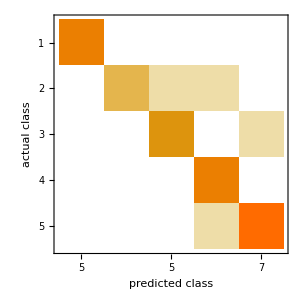

```mathematica
gestMeasurements["ConfusionMatrixPlot"]
```

```mathematica
Export["classifier1to5w25.wmlf",gestClassifier]
```

classifier1to5w25.wmlf

```mathematica
$HomeDirectory
```

/Users/eohomegrownapps